# Computational Project: Spin Wave Simulation and Normal Mode Analysis

## Spin Wave Simulation Using Linearized Heisenberg Interaction

#### Governing equations of the spin states of 3 atoms modeled using the linearized Heisenberg Interaction

```mathematica
Clear[Solution];
Clear[x1, x2, x3, y1, y2, y3, z1, z2, z3];

(* Coupling Constant *)
J = .1;

Solution = NDSolve[
  {
    (* System of equations *)
    x1'[t] == J * (2 * y1[t] - y3[t] - y2[t]) - 1 x1'[t],
    y1'[t] == J * (2 * x1[t] - x3[t] - x2[t]) - 1 y1'[t],
    z1'[t] == 0,

    x2'[t] == J * (2 * y2[t] - y1[t] - y3[t]) - 1 x2'[t],
    y2'[t] == J * (2 * x2[t] - x1[t] - x3[t]) - 1 y2'[t],
    z2'[t] == 0,

    x3'[t] == J * (2 * y3[t] - y2[t] - y1[t]) - 1 x3'[t],
    y3'[t] == J * (2 * x3[t] - x2[t] - x1[t]) - 1 y3'[t],
    z3'[t] == 0,

    (* Initial conditions *)
    x1[0] == 1, y1[0] == 0, z1[0] == 0,
    x2[0] == 0, y2[0] == 1, z2[0] == 0,
    x3[0] == 1, y3[0] == 0, z3[0] == 0
  },
  {x1, y1, z1, x2, y2, z2, x3, y3, z3},
  {t, 0, 300},
  Method -> {"BDF"} (* An attempt to stabilize the system *)
];
```

Note, the governing equations above are not solved as the next examples are as the system is dynamically unstable. This has led me to be unable to solve the equations numerically. Luckily, the closed form solution can be calculated and can be included below.

```mathematica
(* Define the state vector *)
X[t_] := {x1[t], y1[t], z1[t], x2[t], y2[t], z2[t], x3[t], y3[t], z3[t]};

(* Define the matrix A *)
A = {
   {-1, 2 J, 0, 0, -J, 0, 0, -J, 0}, (* x1' equation coefficients *)
   {2 J, -1, 0, -J, 0, 0, -J, 0, 0}, (* y1' equation coefficients *)
   {0, 0, 0, 0, 0, 0, 0, 0, 0},      (* z1' equation coefficients *)
   {0, -J, 0, -1, 2 J, 0, 0, -J, 0}, 
   {-J, 0, 0, 2 J, -1, 0, -J, 0, 0}, 
   {0, 0, 0, 0, 0, 0, 0, 0, 0},      
   {0, -J, 0, 0, -J, 0, -1, 2 J, 0}, 
   {-J, 0, 0, -J, 0, 0, 2 J, -1, 0}, 
   {0, 0, 0, 0, 0, 0, 0, 0, 0}      
};

(* Display the matrix *)
MatrixForm[A]


ω2 = Sqrt[Eigenvalues[A]]
Eigenvectors[A]
```

(-1 | 2 | 0 | 0 | -1 | 0 | 0 | -1 | 0
2 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 2 | 0 | 0 | -1 | 0
-1 | 0 | 0 | 2 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | -1 | 0 | -1 | 2 | 0
-1 | 0 | 0 | -1 | 0 | 0 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{2 ⅈ,2 ⅈ,√2,√2,ⅈ,ⅈ,0,0,0}

{{1,-1,0,0,0,0,-1,1,0},{1,-1,0,-1,1,0,0,0,0},{-1,-1,0,0,0,0,1,1,0},{-1,-1,0,1,1,0,0,0,0},{0,1,0,0,1,0,0,1,0},{1,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0}}

## Summary

Above are the calculated normal modes of the 3 particle system. This system is only valid for small displacements in the x and y direction of spin where we assume the z component of the spin is so small that it can be ignored. The system above is analogous to the a system of blocks whose interactions are modeled by linear springs (with periodic boundary conditions). While this system is nice to work with, it is too simple to model many things in reality. This will require us to take a look at the non-linear system.

## Spin Wave Simulation Through Heisenberg Interaction Without External Magnetic Field

#### Governing Equations of Spin Wave Simulation Without External Magnetic Field

Below are the governing equations for the interaction of particles in the 3 particle system using their non-linear form. Below, I have also included plots to help us visualize what the system is doing under some initial conditions.

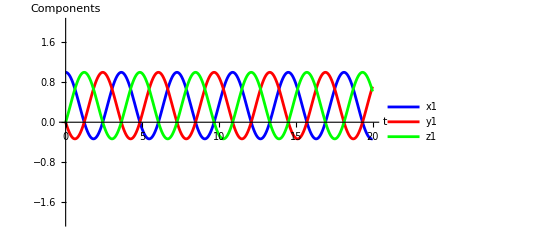

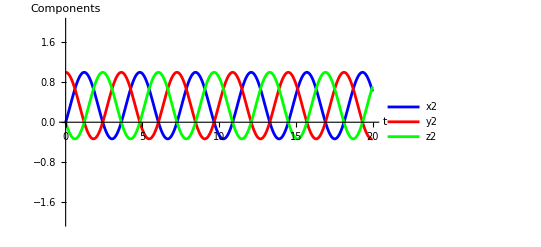

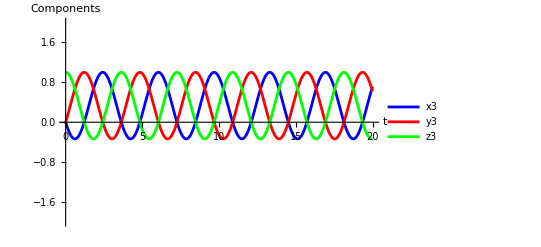

```mathematica
Clear[Solution];
Clear[x1, x2, x3, y1, y2, y3, z1, z2, z3];

(* Coupling constant *)
J = 1;

(* Define the system of differential equations with periodic boundary conditions! *)
Solution = NDSolve[{
   (* Particle 1 *)         
   x1'[t] == J *(y1[t] * (z3[t] + z2[t]) - z1[t] * (y3[t] + y2[t])),
   y1'[t] == J *(z1[t] * (x3[t] + x2[t]) - x1[t] *(z3[t] + z2[t])),
   z1'[t] == J *(x1[t] * (y3[t] + y2[t]) - y1[t] *(x3[t] + x2[t])),
   
   (* Particle 2 *)
   x2'[t] == J *(y2[t] * (z1[t] + z3[t]) - z2[t] * (y1[t] + y3[t])),
   y2'[t] == J *(z2[t] * (x1[t] + x3[t]) - x2[t] * (z1[t] + z3[t])),
   z2'[t] == J *(x2[t] * (y1[t] + y3[t]) - y2[t] * (x1[t] + x3[t])),
   
   (* Particle 3 *)
   x3'[t] == J * (y3[t] * (z2[t] + z1[t]) - z3[t] * (y2[t] + y1[t])),
   y3'[t] == J * (z3[t] * (x2[t] + x1[t]) - x3[t] * (z2[t] + z1[t])),
   z3'[t] == J * (x3[t] * (y2[t] + y1[t]) - y3[t] * (x2[t] + x1[t])),
   
   (* Initial conditions *)
   x1[0] == 1, y1[0] == 0, z1[0] == 0,
   x2[0] == 0, y2[0] == 1, z2[0] == 0,
   x3[0] == 0, y3[0] == 0, z3[0] == 1
   },
  {x1, y1, z1, x2, y2, z2, x3, y3, z3}, {t, 0, 100}];

Plot[
  Evaluate[{x1[t], y1[t], z1[t]} /. Solution], {t, 0, 20}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x1", "y1", "z1"}
]

Plot[
  Evaluate[{x2[t], y2[t], z2[t]} /. Solution], {t, 0, 20}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x2", "y2", "z2"}
]

Plot[
  Evaluate[{x3[t], y3[t], z3[t]} /. Solution], {t, 0, 20}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x3", "y3", "z3"}
]

Manipulate[
 Graphics3D[
  {
   (* Current vector with First for coordinates *)
   Green, Arrow[{{0, 0, 0}, {First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}}], (* Current vector *)
   
   (* Current point *)
   Green, PointSize[Large], 
   Point[{First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}],
   
   (* Trace line for first coordinates *)
   Black, 
   Line[Table[{First[x1[s] /. Solution], First[y1[s] /. Solution], First[z1[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   (* Second vector and point with First for coordinates *)
   Blue, Arrow[{{0, 0, 0}, {First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}}],
   Blue, PointSize[Large], Point[{First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}],
   Black, Line[Table[{First[x2[s] /. Solution], First[y2[s] /. Solution], First[z2[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   
   Red, Arrow[{{0, 0, 0}, {First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}}],
   Red, PointSize[Large], Point[{First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}],
   Black, Line[Table[{First[x3[s] /. Solution], First[y3[s] /. Solution], First[z3[s] /. Solution]}, {s, 0, t, 0.1}]]
  },
  Boxed -> False,
  Axes -> True,
  AxesOrigin -> {0, 0, 0},
  AxesLabel -> {"x1", "y1", "z1"},
  ViewPoint -> Dynamic[vp], 
  PlotRange -> {{-2, 2}, {-2, 2}, {-2, 2}}
 ],
 {{t, 0}, 0, 20, AnimationRate -> 0.5},
 Initialization :> (vp = {1.3, -2.4, 2.0}), 
 TrackedSymbols :> {t, vp}
]
```

As shown above, we find that the system is oscillatory. The coordinates are periodic, giving us our first look at a magnon!

#### Spin Wave Simulation

```mathematica
Manipulate[
 Graphics3D[
  {
   (* Particles *)
   Blue, Sphere[{0, 0, 0}, 0.2],
   Red, Sphere[{1, 0, 0}, 0.2],
   Green, Sphere[{-1, 0, 0}, 0.2],
   
  
   Green, Arrow[Tube[{{-1, 0, 0}, 
     {-1, 0, 0} + ScalingFactor * {First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}}, TubeThickness]],
   Blue, Arrow[Tube[{{0, 0, 0}, 
     {0, 0, 0} + ScalingFactor * {First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}}, TubeThickness]],
   Red, Arrow[Tube[{{1, 0, 0}, 
     {1, 0, 0} + ScalingFactor * {First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}}, TubeThickness]]
  },
  Boxed -> True,
  Axes -> True,
  PlotRange -> {{-zoom, zoom}, {-zoom, zoom}, {-zoom, zoom}}, 
  AxesOrigin -> {0, 0, 0},
  AxesLabel -> {"x", "y", "z"},
  ViewPoint -> {1, -2, 2}
 ],
 {{t, 0}, 0, 100, 0.1},            
 {{zoom, 2}, 1, 10, 0.1},         
 {{ScalingFactor, 0.5}, 0.1, 1, 0.05}, 
 {{TubeThickness, 0.1}, 0.01, 0.5, 0.01} 
]
```

To give us a better sense of what is going on in this system, I have included an illustration above that allows us to visualize the spin of the particles as they undergo periodic oscillations.

## Spin Wave Simulation Through Heisenberg Interaction With External Magnetic Field

#### Governing Equations of the 3 Particle System’s Spin Using the Heisenberg Interaction Under the Influence of an External Magnetic Field

Next, what if we were to add a magnetic field along the z-axis of the system? This is something commonly done when modeling materials and will give us a sense of how well our models holds to reality.

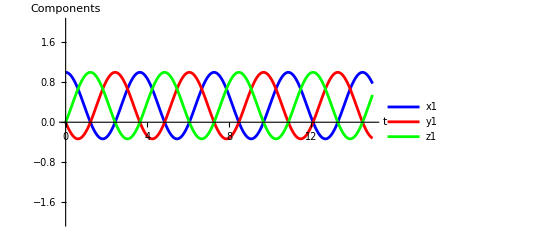

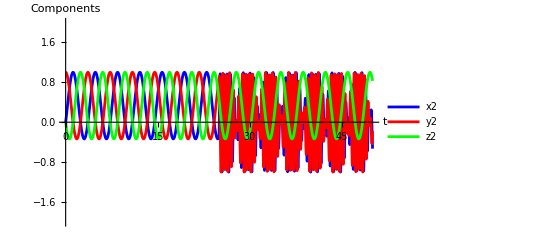

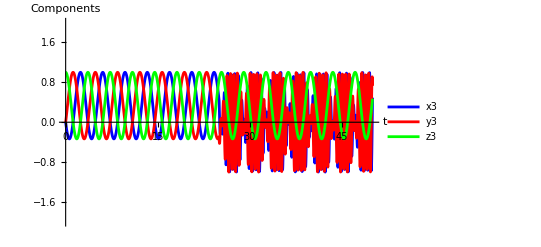

```mathematica
Clear[Solution];
Clear[x1, x2, x3, y1, y2, y3, z1, z2, z3];

(* Everything still needs to be non-dimensionalized *)
(* Coupling constant and magnetic field parameters *)
J = 1; (* Coupling constant *)
gamma = 1; (* Gyromagnetic ratio *)
Bz = 10; (* Strength of the magnetic field *)
ton = 25; (* Time when the magnetic field turns on *)
Bz = 10;
gamma = 1;

(* System of equations with time-dependent magnetic field *)
Solution = NDSolve[{
   (* Particle 1 with time-dependent magnetic field *)
   x1'[t] == J * (y1[t] * (z3[t] + z2[t]) - z1[t] * (y3[t] + y2[t])) 
               + gamma * (y1[t] * Bz * UnitStep[t - ton]),
   y1'[t] == J * (z1[t] * (x3[t] + x2[t]) - x1[t] * (z3[t] + z2[t])) 
               - gamma * (x1[t] * Bz * UnitStep[t - ton]),
   z1'[t] == J * (x1[t] * (y3[t] + y2[t]) - y1[t] * (x3[t] + x2[t])),

   (* Particle 2 with time-dependent magnetic field *)
   x2'[t] == J * (y2[t] * (z1[t] + z3[t]) - z2[t] * (y1[t] + y3[t])) 
               + gamma * (y2[t] * Bz * UnitStep[t - ton]),
   y2'[t] == J * (z2[t] * (x1[t] + x3[t]) - x2[t] * (z1[t] + z3[t])) 
               - gamma * (x2[t] * Bz * UnitStep[t - ton]),
   z2'[t] == J * (x2[t] * (y1[t] + y3[t]) - y2[t] * (x1[t] + x3[t])),

   (* Particle 3 with time-dependent magnetic field *)
   x3'[t] == J * (y3[t] * (z2[t] + z1[t]) - z3[t] * (y2[t] + y1[t])) 
               + gamma * (y3[t] * Bz * UnitStep[t - ton]),
   y3'[t] == J * (z3[t] * (x2[t] + x1[t]) - x3[t] * (z2[t] + z1[t])) 
               - gamma * (x3[t] * Bz * UnitStep[t - ton]),
   z3'[t] == J * (x3[t] * (y2[t] + y1[t]) - y3[t] * (x2[t] + x1[t])),

   (* Initial conditions *)
   x1[0] == 1, y1[0] == 0, z1[0] == 0,
   x2[0] == 0, y2[0] == 1, z2[0] == 0,
   x3[0] == 0, y3[0] == 0, z3[0] == 1
   },
  {x1, y1, z1, x2, y2, z2, x3, y3, z3}, {t, 0, 50}];


Plot[
  Evaluate[{x1[t], y1[t], z1[t]} /. Solution], {t, 0, 15}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x1", "y1", "z1"}
]

Plot[
  Evaluate[{x2[t], y2[t], z2[t]} /. Solution], {t, 0, 50}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x2", "y2", "z2"}
]

Plot[
  Evaluate[{x3[t], y3[t], z3[t]} /. Solution], {t, 0, 50}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x3", "y3", "z3"}
]


Manipulate[
 Graphics3D[
  {
   
   Green, Arrow[{{0, 0, 0}, {First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}}], (* Current vector *) 
   Green, PointSize[Large], 
   Point[{First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}],
   Black, 
   Line[Table[{First[x1[s] /. Solution], First[y1[s] /. Solution], First[z1[s] /. Solution]}, {s, 0, t, 0.1}]],

   Blue, Arrow[{{0, 0, 0}, {First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}}],
   Blue, PointSize[Large], Point[{First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}],
   Black, Line[Table[{First[x2[s] /. Solution], First[y2[s] /. Solution], First[z2[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   
   Red, Arrow[{{0, 0, 0}, {First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}}],
   Red, PointSize[Large], Point[{First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}],
   Black, Line[Table[{First[x3[s] /. Solution], First[y3[s] /. Solution], First[z3[s] /. Solution]}, {s, 0, t, 0.1}]]
  },
  Boxed -> False,
  Axes -> True,
  AxesOrigin -> {0, 0, 0},
  AxesLabel -> {"x1", "y1", "z1"},
  ViewPoint -> Dynamic[vp], (* Enable interactive orbit controls *)
  PlotRange -> {{-2, 2}, {-2, 2}, {-2, 2}}
 ],
 {{t, 0}, 0, 50, AnimationRate -> 0.5},
 Initialization :> (vp = {1.3, -2.4, 2.0}), (* Initial viewpoint for the plot *)
 TrackedSymbols :> {t, vp}
]
```

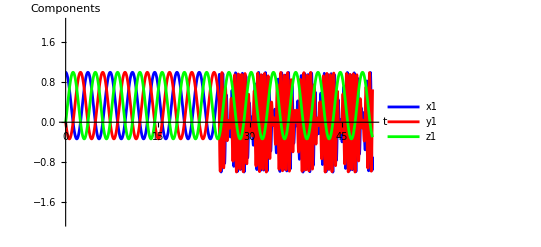

-Graphics-

-Graphics-

As shown above, we can easily spot when the magnetic field is turned on. In particular, when the magnetic field is turned on we find that the system undergoes what seems to be resonating with the magnetic field. This is indicated by the wave-packets shown in the coordinates. Furthermore, from our interactive graph, we see that the system becomes quasi-periodic!

```mathematica
Manipulate[
 Graphics3D[
  {
   (* Particles *)
   Red, Sphere[{1, 0, 0}, 0.2],
   Green, Sphere[{-1, 0, 0}, 0.2],
   Blue, Sphere[{0, 0, 0}, 0.2],
   
   (* Scaled and thicker moving vectors *)
   Green, Arrow[Tube[{{-1, 0, 0}, 
     {-1, 0, 0} + ScalingFactor * {First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}}, TubeThickness]],
   Blue, Arrow[Tube[{{0, 0, 0}, 
     {0, 0, 0} + ScalingFactor * {First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}}, TubeThickness]],
   Red, Arrow[Tube[{{1, 0, 0}, 
     {1, 0, 0} + ScalingFactor * {First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}}, TubeThickness]]
  },
  Boxed -> True,
  Axes -> True,
  PlotRange -> {{-zoom, zoom}, {-zoom, zoom}, {-zoom, zoom}}, (* Dynamic zoom *)
  AxesOrigin -> {0, 0, 0},
  AxesLabel -> {"x", "y", "z"},
  ViewPoint -> {1, -2, 2}
 ],
 {{t, 0}, 0, 50, 0.1},            (* Time range *)
 {{zoom, 2}, 1, 10, 0.1},         (* Zoom range *)
 {{ScalingFactor, 0.5}, 0.1, 1, 0.05}, (* Scaling factor for arrow length *)
 {{TubeThickness, 0.1}, 0.01, 0.5, 0.01} (* Thickness of the tubes *)
]
```

Above is another illustration to help us get a better sense of what is going on. But upon further inspection, something appears to be wrong. When a magnetic field is applied to materials like iron, the spins overtime align with the magnetic field. This model does not include any terms to represent damping, leading to the system conserving quantities like angular momentum. To model this behavior requires a new model, but first let us explore how to calculate the normal modes of the non-linear system.

## Normal Mode Analysis of Spin Wave Simulation

```mathematica
(* Define the system of differential equations with initial conditions *)
J = 1; (* Example value for J, change as needed *)
system = {
   (* Particle 1 with time-dependent magnetic field *)
   x1'[t] == J * (y1[t] * (z3[t] + z2[t]) - z1[t] * (y3[t] + y2[t])) 
               + gamma * (y1[t] * Bz),
   y1'[t] == J * (z1[t] * (x3[t] + x2[t]) - x1[t] * (z3[t] + z2[t])) 
               - gamma * (x1[t] * Bz),
   z1'[t] == J * (x1[t] * (y3[t] + y2[t]) - y1[t] * (x3[t] + x2[t])),

   (* Particle 2 with time-dependent magnetic field *)
   x2'[t] == J * (y2[t] * (z1[t] + z3[t]) - z2[t] * (y1[t] + y3[t])) 
               + gamma * (y2[t] * Bz),
   y2'[t] == J * (z2[t] * (x1[t] + x3[t]) - x2[t] * (z1[t] + z3[t])) 
               - gamma * (x2[t] * Bz),
   z2'[t] == J * (x2[t] * (y1[t] + y3[t]) - y2[t] * (x1[t] + x3[t])),

   (* Particle 3 with time-dependent magnetic field *)
   x3'[t] == J * (y3[t] * (z2[t] + z1[t]) - z3[t] * (y2[t] + y1[t])) 
               + gamma * (y3[t] * Bz),
   y3'[t] == J * (z3[t] * (x2[t] + x1[t]) - x3[t] * (z2[t] + z1[t])) 
               - gamma * (x3[t] * Bz),
   z3'[t] == J * (x3[t] * (y2[t] + y1[t]) - y3[t] * (x2[t] + x1[t])),
   
   (* Initial conditions *)
   x1[0] == 1, y1[0] == 0, z1[0] == 0,
   x2[0] == 0, y2[0] == 1, z2[0] == 0,
   x3[0] == 0, y3[0] == 0, z3[0] == 1
   };

(* Numerical solution *)
solution = NDSolve[
   system,
   {x1, y1, z1, x2, y2, z2, x3, y3, z3}, {t, 0, 100}
   ];

(* Linearization around equilibrium points *)
(* Solve for equilibrium points *)
equilibriumPoints = Solve[
   {
    J*(y1*(z3 + z2) - z1*(y3 + y2)) == 0,
    J*(z1*(x3 + x2) - x1*(z3 + z2)) == 0,
    J*(x1*(y3 + y2) - y1*(x3 + x2)) == 0,
    J*(y2*(z1 + z3) - z2*(y1 + y3)) == 0,
    J*(z2*(x1 + x3) - x2*(z1 + z3)) == 0,
    J*(x2*(y1 + y3) - y2*(x1 + x3)) == 0,
    J*(y3*(z2 + z1) - z3*(y2 + y1)) == 0,
    J*(z3*(x2 + x1) - x3*(z2 + z1)) == 0,
    J*(x3*(y2 + y1) - y3*(x2 + x1)) == 0
   },
   {x1, y1, z1, x2, y2, z2, x3, y3, z3}
   ];

(* CHECK with Prof. Tamayo if this is correct*)
(* Compute the Jacobian matrix *)
jacobian = D[
   {
    J*(y1*(z3 + z2) - z1*(y3 + y2)),
    J*(z1*(x3 + x2) - x1*(z3 + z2)),
    J*(x1*(y3 + y2) - y1*(x3 + x2)),
    J*(y2*(z1 + z3) - z2*(y1 + y3)),
    J*(z2*(x1 + x3) - x2*(z1 + z3)),
    J*(x2*(y1 + y3) - y2*(x1 + x3)),
    J*(y3*(z2 + z1) - z3*(y2 + y1)),
    J*(z3*(x2 + x1) - x3*(z2 + z1)),
    J*(x3*(y2 + y1) - y3*(x2 + x1))
   },
   {{x1, y1, z1, x2, y2, z2, x3, y3, z3}}
   ];

(* Evaluate Jacobian at an equilibrium point *)
linearizedJacobian = jacobian /. equilibriumPoints[[1]];

(* Eigenvalues and eigenvectors for the Jacobian *)
eigenvalues = Eigenvalues[linearizedJacobian];
eigenvectors = Eigenvectors[linearizedJacobian];

(* Not exactly part of the project, but this seemed very interesting and wanted to see what the output was *)
(* Fourier analysis of numerical solution *)
x1sol = x1 /. First[solution];
dataX1 = Table[x1sol[t], {t, 0, 100, 0.1}];
frequencies = Abs[Fourier[dataX1]];

(* Outputs *)
{EquilibriumPoints, eigenvectors}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{EquilibriumPoints,{{0,0,-1,0,0,0,0,0,1},{0,-1,0,0,0,0,0,1,0},{-1,0,0,0,0,0,1,0,0},{0,0,-1,0,0,1,0,0,0},{0,-1,0,0,1,0,0,0,0},{-1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}}

## Six Particle System

1

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],z2→InterpolatingFunction[…],x3→InterpolatingFunction[…],y3→InterpolatingFunction[…],z3→InterpolatingFunction[…],x4→InterpolatingFunction[…],y4→InterpolatingFunction[…],z4→InterpolatingFunction[…],x5→InterpolatingFunction[…],y5→InterpolatingFunction[…],z5→InterpolatingFunction[…],x6→InterpolatingFunction[…],y6→InterpolatingFunction[…],z6→InterpolatingFunction[…]}}

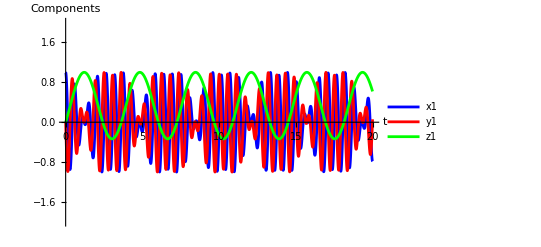

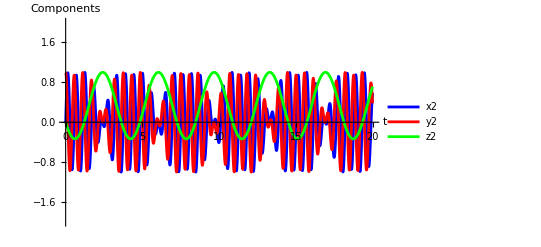

```mathematica
Clear[Solution];
Clear[x1, x2, x3, x4, x5, x6, y1, y2, y3, y4, y5, y6, z1, z2, z3, z4, z5, z6];

Bz = 10;  (* Example magnetic field strength in the z-direction *)
J = 1

Solution = NDSolve[{
   (* Particle 1 with magnetic field interaction *)
   x1'[t] == J * (y1[t] * (z3[t] + z2[t]) - z1[t] * (y3[t] + y2[t])) + gamma * (y1[t] * Bz),
   y1'[t] == J * (z1[t] * (x3[t] + x2[t]) - x1[t] * (z3[t] + z2[t])) - gamma * (x1[t] * Bz),
   z1'[t] == J * (x1[t] * (y3[t] + y2[t]) - y1[t] * (x3[t] + x2[t])),

   (* Particle 2 with magnetic field interaction *)
   x2'[t] == J * (y2[t] * (z1[t] + z3[t]) - z2[t] * (y1[t] + y3[t])) + gamma * (y2[t] * Bz),
   y2'[t] == J * (z2[t] * (x1[t] + x3[t]) - x2[t] * (z1[t] + z3[t])) - gamma * (x2[t] * Bz),
   z2'[t] == J * (x2[t] * (y1[t] + y3[t]) - y2[t] * (x1[t] + x3[t])),

   (* Particle 3 with magnetic field interaction *)
   x3'[t] == J * (y3[t] * (z2[t] + z1[t]) - z3[t] * (y2[t] + y1[t])) + gamma * (y3[t] * Bz),
   y3'[t] == J * (z3[t] * (x2[t] + x1[t]) - x3[t] * (z2[t] + z1[t])) - gamma * (x3[t] * Bz),
   z3'[t] == J * (x3[t] * (y2[t] + y1[t]) - y3[t] * (x2[t] + x1[t])),

   (* Particle 4 with magnetic field interaction *)
   x4'[t] == J * (y4[t] * (z1[t] + z2[t]) - z4[t] * (y1[t] + y2[t])) + gamma * (y4[t] * Bz),
   y4'[t] == J * (z4[t] * (x1[t] + x2[t]) - x4[t] * (z1[t] + z2[t])) - gamma * (x4[t] * Bz),
   z4'[t] == J * (x4[t] * (y1[t] + y2[t]) - y4[t] * (x1[t] + x2[t])),

   (* Particle 5 with magnetic field interaction *)
   x5'[t] == J * (y5[t] * (z2[t] + z3[t]) - z5[t] * (y2[t] + y3[t])) + gamma * (y5[t] * Bz),
   y5'[t] == J * (z5[t] * (x2[t] + x3[t]) - x5[t] * (z2[t] + z3[t])) - gamma * (x5[t] * Bz),
   z5'[t] == J * (x5[t] * (y2[t] + y3[t]) - y5[t] * (x2[t] + x3[t])),

   (* Particle 6 with magnetic field interaction *)
   x6'[t] == J * (y6[t] * (z3[t] + z1[t]) - z6[t] * (y3[t] + y1[t])) + gamma * (y6[t] * Bz),
   y6'[t] == J * (z6[t] * (x3[t] + x1[t]) - x6[t] * (z3[t] + z1[t])) - gamma * (x6[t] * Bz),
   z6'[t] == J * (x6[t] * (y3[t] + y1[t]) - y6[t] * (x3[t] + x1[t])),

   (* Initial conditions *)
   x1[0] == 1, y1[0] == 0, z1[0] == 0,
   x2[0] == 0, y2[0] == 1, z2[0] == 0,
   x3[0] == 0, y3[0] == 0, z3[0] == 1,
   x4[0] == 0, y4[0] == 1, z4[0] == 0,
   x5[0] == 1, y5[0] == 0, z5[0] == 0,
   x6[0] == 0, y6[0] == 0, z6[0] == 1
   },
  {x1, y1, z1, x2, y2, z2, x3, y3, z3, x4, y4, z4, x5, y5, z5, x6, y6, z6}, {t, 0, 50}]

(* Plotting each particle's position *)
Plot[
  Evaluate[{x1[t], y1[t], z1[t]} /. Solution], {t, 0, 20}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x1", "y1", "z1"}
]

Plot[
  Evaluate[{x2[t], y2[t], z2[t]} /. Solution], {t, 0, 20}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x2", "y2", "z2"}
]


Manipulate[
 Graphics3D[
  {
   (* Particle 1 *)
   Green, Arrow[{{0, 0, 0}, {First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}}], 
   Green, PointSize[Large], 
   Point[{First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}],
   Black, Line[Table[{First[x1[s] /. Solution], First[y1[s] /. Solution], First[z1[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   (* Particle 2 *)
   Blue, Arrow[{{0, 0, 0}, {First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}}],
   Blue, PointSize[Large], Point[{First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}],
   Black, Line[Table[{First[x2[s] /. Solution], First[y2[s] /. Solution], First[z2[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   (* Particle 3 *)
   Red, Arrow[{{0, 0, 0}, {First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}}],
   Red, PointSize[Large], Point[{First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}],
   Black, Line[Table[{First[x3[s] /. Solution], First[y3[s] /. Solution], First[z3[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   (* Particle 4 *)
   Purple, Arrow[{{0, 0, 0}, {First[x4[t] /. Solution], First[y4[t] /. Solution], First[z4[t] /. Solution]}}],
   Purple, PointSize[Large], Point[{First[x4[t] /. Solution], First[y4[t] /. Solution], First[z4[t] /. Solution]}],
   Black, Line[Table[{First[x4[s] /. Solution], First[y4[s] /. Solution], First[z4[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   (* Particle 5 *)
   Orange, Arrow[{{0, 0, 0}, {First[x5[t] /. Solution], First[y5[t] /. Solution], First[z5[t] /. Solution]}}],
   Orange, PointSize[Large], Point[{First[x5[t] /. Solution], First[y5[t] /. Solution], First[z5[t] /. Solution]}],
   Black, Line[Table[{First[x5[s] /. Solution], First[y5[s] /. Solution], First[z5[s] /. Solution]}, {s, 0, t, 0.1}]],
   
   (* Particle 6 *)
   Yellow, Arrow[{{0, 0, 0}, {First[x6[t] /. Solution], First[y6[t] /. Solution], First[z6[t] /. Solution]}}],
   Yellow, PointSize[Large], Point[{First[x6[t] /. Solution], First[y6[t] /. Solution], First[z6[t] /. Solution]}],
   Black, Line[Table[{First[x6[s] /. Solution], First[y6[s] /. Solution], First[z6[s] /. Solution]}, {s, 0, t, 0.1}]]
  },
  Boxed -> False,
  Axes -> True,
  AxesOrigin -> {0, 0, 0},
  AxesLabel -> {"x", "y", "z"},
  ViewPoint -> Dynamic[vp], 
  PlotRange -> {{-2, 2}, {-2, 2}, {-2, 2}},
  Lighting -> "Neutral"
 ],
 {{t, 0}, 0, 20, AnimationRate -> 0.5},
 Initialization :> (vp = {1.3, -2.4, 2.0}), 
 TrackedSymbols :> {t, vp}
]
```

```mathematica
Manipulate[
 Graphics3D[
  {
   (*Note to self; make sure that the particles are correctly ordered*)
   Blue, Sphere[{-2, 0, 0}, 0.2],   (* Particle 1 at x = -2 *)
   Red, Sphere[{-1, 0, 0}, 0.2],    (* Particle 2 at x = -1 *)
   Green, Sphere[{0, 0, 0}, 0.2],   (* Particle 3 at x = 0 *)
   Purple, Sphere[{1, 0, 0}, 0.2],  (* Particle 4 at x = 1 *)
   Orange, Sphere[{2, 0, 0}, 0.2], (* Particle 5 at x = 2 *)
   Yellow, Sphere[{3, 0, 0}, 0.2], (* Particle 6 at x = 3 *)
   
   (* Scaled and thicker moving vectors along the x-axis with matching colors *)
   Blue, Arrow[Tube[{{-2, 0, 0}, 
     {-2, 0, 0} + ScalingFactor * {First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}}, TubeThickness]],
   Red, Arrow[Tube[{{-1, 0, 0}, 
     {-1, 0, 0} + ScalingFactor * {First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}}, TubeThickness]],
   Green, Arrow[Tube[{{0, 0, 0}, 
     {0, 0, 0} + ScalingFactor * {First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}}, TubeThickness]],
   Purple, Arrow[Tube[{{1, 0, 0}, 
     {1, 0, 0} + ScalingFactor * {First[x4[t] /. Solution], First[y4[t] /. Solution], First[z4[t] /. Solution]}}, TubeThickness]],
   Orange, Arrow[Tube[{{2, 0, 0}, 
     {2, 0, 0} + ScalingFactor * {First[x5[t] /. Solution], First[y5[t] /. Solution], First[z5[t] /. Solution]}}, TubeThickness]],
   Yellow, Arrow[Tube[{{3, 0, 0}, 
     {3, 0, 0} + ScalingFactor * {First[x6[t] /. Solution], First[y6[t] /. Solution], First[z6[t] /. Solution]}}, TubeThickness]]
  },
  Boxed -> True,
  Axes -> True,
  PlotRange -> {{-zoom, 5}, {-zoom, zoom}, {-zoom, zoom}}, (* Extended plot range to fit all particles *)
  AxesOrigin -> {0, 0, 0},
  AxesLabel -> {"x", "y", "z"},
  ViewPoint -> {1, -2, 2}
 ],
 {{t, 0}, 0, 20, 0.1},            
 {{zoom, 2}, 1, 10, 0.1},         
 {{ScalingFactor, 0.5}, 0.1, 1, 0.05}, 
 {{TubeThickness, 0.1}, 0.01, 0.5, 0.01} 
]
```

## Landau-Lifshitz-Gilbert (LLG) Equation

#### The Governing Equations of the 3 Particle System Using the Landau-Lifshitz-Gilbert (LLG) Model of Spin

As mentioned above, the Heisenberg model was unable to capture the phenomenon of particles aligning themselves in the direction of a magnetic field. This model includes damping to the environment that helps account for this phenomenon.

1

-Graphics3D-

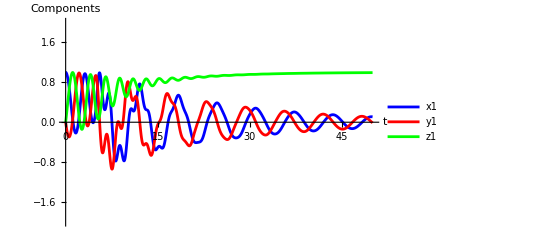

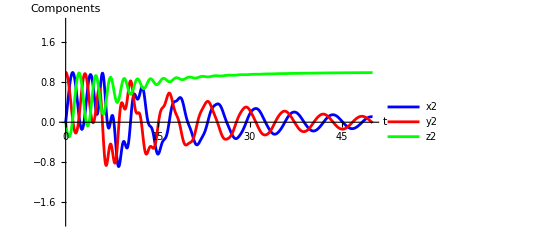

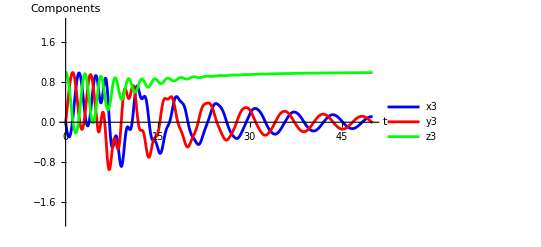

```mathematica
Clear[Solution]
Clear[x1, y1, z1, x2, y2, z2, x3, y3, z3]

(* Non-dimensionalized parameters (hopefully) *)
J = 1; (* Exchange coupling constant (non-dimensionalized; hopefully) *)
gamma = 1; (* Gyromagnetic ratio (will explain what this is in paper) *)
alpha = 0.05; (* Damping coefficient *)
Bz = 1; (* Magnetic field in the z-direction *)

t0 = 1
tFieldOn = 5 * t0; (* Time to turn on magnetic field *)

(* Magnetic field activation step function (dimensionless - I think) *)
BzActive[t_] := UnitStep[t - tFieldOn];


Solution = NDSolve[{
   (* Particle 1 *)
   x1'[t] == J*(y1[t]*(z3[t] + z2[t]) - z1[t]*(y3[t] + y2[t])) + 
              (y1[t]*BzActive[t]) - alpha*((y1[t]*z1'[t]) - (z1[t]*y1'[t])),
   y1'[t] == J*(z1[t]*(x3[t] + x2[t]) - x1[t]*(z3[t] + z2[t])) - 
              (x1[t]*BzActive[t]) - alpha*((z1[t]*x1'[t]) - (x1[t]*z1'[t])),
   z1'[t] == J*(x1[t]*(y3[t] + y2[t]) - y1[t]*(x3[t] + x2[t])) - 
              alpha*((x1[t]*y1'[t]) - (y1[t]*x1'[t])),

   (* Particle 2 *)
   x2'[t] == J*(y2[t]*(z1[t] + z3[t]) - z2[t]*(y1[t] + y3[t])) + 
              (y2[t]*BzActive[t]) - alpha*((y2[t]*z2'[t]) - (z2[t]*y2'[t])),
   y2'[t] == J*(z2[t]*(x1[t] + x3[t]) - x2[t]*(z1[t] + z3[t])) - 
              (x2[t]*BzActive[t]) - alpha*((z2[t]*x2'[t]) - (x2[t]*z2'[t])),
   z2'[t] == J*(x2[t]*(y1[t] + y3[t]) - y2[t]*(x1[t] + x3[t])) - 
              alpha*((x2[t]*y2'[t]) - (y2[t]*x2'[t])),

   (* Particle 3 *)
   x3'[t] == J*(y3[t]*(z2[t] + z1[t]) - z3[t]*(y2[t] + y1[t])) + 
              (y3[t]*BzActive[t]) - alpha*((y3[t]*z3'[t]) - (z3[t]*y3'[t])),
   y3'[t] == J*(z3[t]*(x2[t] + x1[t]) - x3[t]*(z2[t] + z1[t])) - 
              (x3[t]*BzActive[t]) - alpha*((z3[t]*x3'[t]) - (x3[t]*z3'[t])),
   z3'[t] == J*(x3[t]*(y2[t] + y1[t]) - y3[t]*(x2[t] + x1[t])) - 
              alpha*((x3[t]*y3'[t]) - (y3[t]*x3'[t])),

   (* Initial conditions *)
   x1[0] == 1, y1[0] == 0.0000001, z1[0] == 0.0000001,
   x2[0] == 0.0000001, y2[0] == 1, z2[0] == 0.0000001,
   x3[0] == 0.0000001, y3[0] == 0.0000001, z3[0] == 1
   },
  {x1, y1, z1, x2, y2, z2, x3, y3, z3}, {t, 0, 100}];

(* Visualization of the spins *)
ParametricPlot3D[
 Evaluate[{{x1[t], y1[t], z1[t]}, {x2[t], y2[t], z2[t]}, {x3[t], y3[t], z3[t]}} /. Solution],
 {t, 0, 100},
 PlotRange -> All,
 AxesLabel -> {"x", "y", "z"},
 PlotLegends -> {"Spin 1", "Spin 2", "Spin 3"},
 Boxed -> True
]



Plot[
  Evaluate[{x1[t], y1[t], z1[t]} /. Solution], {t, 0, 50}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x1", "y1", "z1"}
]

Plot[
  Evaluate[{x2[t], y2[t], z2[t]} /. Solution], {t, 0, 50}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x2", "y2", "z2"}
]

Plot[
  Evaluate[{x3[t], y3[t], z3[t]} /. Solution], {t, 0, 50}, 
  PlotStyle -> {Blue, Red, Green}, 
  TicksStyle -> Directive[Black, 20],
  AxesStyle -> {{Thick, Black}, {Thick, Black}},
  PlotRange -> 2, AxesOrigin -> {0, 0},
  AxesLabel -> {
    Style["t", Black, Italic, 30], 
    Style["Components", Black, Italic, 20]
  },
  PlotLegends -> {"x3", "y3", "z3"}
]
```

As shown above, our model behaves as we’d expect! While the model does undergo oscillations, these oscillations soon die out and the spin aligns itself with the magnetic field. Amazing!

```mathematica
Manipulate[
 Graphics3D[
  {
   
   Red, Sphere[{1, 0, 0}, 0.2],
   Green, Sphere[{-1, 0, 0}, 0.2],
   Blue, Sphere[{0, 0, 0}, 0.2],
   
   (* Scaled and thicker moving vectors *)
   Green, Arrow[Tube[{{-1, 0, 0}, 
     {-1, 0, 0} + ScalingFactor * {First[x1[t] /. Solution], First[y1[t] /. Solution], First[z1[t] /. Solution]}}, TubeThickness]],
   Blue, Arrow[Tube[{{0, 0, 0}, 
     {0, 0, 0} + ScalingFactor * {First[x2[t] /. Solution], First[y2[t] /. Solution], First[z2[t] /. Solution]}}, TubeThickness]],
   Red, Arrow[Tube[{{1, 0, 0}, 
     {1, 0, 0} + ScalingFactor * {First[x3[t] /. Solution], First[y3[t] /. Solution], First[z3[t] /. Solution]}}, TubeThickness]]
  },
  Boxed -> True,
  Axes -> True,
  PlotRange -> {{-zoom, zoom}, {-zoom, zoom}, {-zoom, zoom}}, (* Dynamic zoom *)
  AxesOrigin -> {0, 0, 0},
  AxesLabel -> {"x", "y", "z"},
  ViewPoint -> {1, -2, 2}
 ],
 {{t, 0}, 0, 50, 0.1},            (* Time range *)
 {{zoom, 2}, 1, 10, 0.1},         (* Zoom range *)
 {{ScalingFactor, 0.5}, 0.1, 1, 0.05}, (* Scaling factor for arrow length *)
 {{TubeThickness, 0.1}, 0.01, 0.5, 0.01} (* Thickness of the tubes *)
]
```

Above, we can see that the model is not only able to recover the previous model’s oscillatory behavior, but it is also able to correctly capture the behavior of the particle’s when the magnetic field is turned on. Since the system includes damping whether or not a magnetic field is induced, we see that the particles are no longer forever excited and at some point, return to an unexcited state!